```mathematica
点光源的情况
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

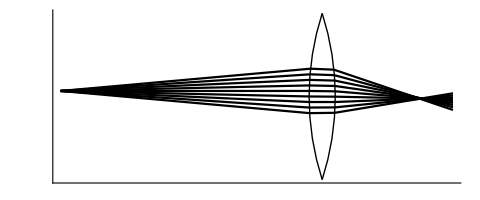

```mathematica
R=100.;a=5.;n1=n3=1;n2=3;yb=√(a*(2R-a));
light={};θm=5π/180.0;y0=yb/15;
Do[
k1={Cos[θ0],-Sin[θ0]};p1={-R,y0};
equ1={ y==p1[[2]]+k1[[2]]/k1[[1]]*(z-p1[[1]]),
y^2+(z-R+a)^2==R^2 };
s=Solve[equ1,{z,y}];
m=z/.s;s=Select[s,(z/.#)==Min[m]&];
p2={z,y}/.s[[1]];
k=
(n1*k1[[2]]*
(p2[[2]]*k1[[2]]+(p2[[1]]-R+a)*k1[[1]])+
(n2-n1)*p2[[2]])/
(n1*k1[[1]]*
(p2[[2]]*k1[[2]]+(p2[[1]]-R+a)*k1[[1]])+
(n2-n1)*(p2[[1]]-R+a));
kz=1/√(1+k^2);ky=k*kz;k2={kz,ky};
equ2={ y==p2[[2]]+k2[[2]]/k2[[1]]*(z-p2[[1]]),
y^2+(z+R-a)^2==R^2 };
s=Solve[equ2,{z,y}];
m=z/.s;s=Select[s,(z/.#)==Max[m]&];
p3={z,y}/.s[[1]];
k=
(n2*k2[[2]]*
(p3[[2]]*k2[[2]]+(p3[[1]]+R-a)*k2[[1]])+
(n3-n2)*p3[[2]])/
(n2*k2[[1]]*
(p3[[2]]*k2[[2]]+(p3[[1]]+R-a)*k2[[1]])+
(n3-n2)*(p3[[1]]+R-a));
y=p3[[2]]+k*(z-p3[[1]]);
p4={z,y}/.z->R/2;
g=Show[
Graphics[{Thickness[0.004],
Line[{p1,p2,p3,p4}]}]];
AppendTo[light,g];Clear[y,z],{θ0,-θm,θm,θm/4}]
θ=ArcSin[yb/R];
Show[light,
Epilog->{Thick,Circle[{R-a,0},R,{π-θ,π+θ}],
Circle[{-R+a,0},R,{-θ,θ}]},
PlotRange->{{-R,R/2},{-yb,yb}},Ticks->None,
Axes->True,AxesStyle->Thickness[0.003]]
Clear[R,y,z,θm,θ,equ1,equ2,light,fig,s]
```

```mathematica
扩大入射范围,不能汇聚到一点
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

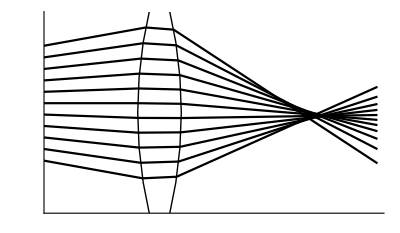

```mathematica
R=100.;a=5.;n1=n3=1;n2=3;yb=√(a*(2R-a));
light={};θm=10π/180.0;y0=yb/15;
Do[
k1={Cos[θ0],-Sin[θ0]};p1={-R,y0};
equ1={ y==p1[[2]]+k1[[2]]/k1[[1]]*(z-p1[[1]]),
y^2+(z-R+a)^2==R^2 };
s=Solve[equ1,{z,y}];
m=z/.s;s=Select[s,(z/.#)==Min[m]&];
p2={z,y}/.s[[1]];
k=
(n1*k1[[2]]*
(p2[[2]]*k1[[2]]+(p2[[1]]-R+a)*k1[[1]])+
(n2-n1)*p2[[2]])/
(n1*k1[[1]]*
(p2[[2]]*k1[[2]]+(p2[[1]]-R+a)*k1[[1]])+
(n2-n1)*(p2[[1]]-R+a));
kz=1/√(1+k^2);ky=k*kz;k2={kz,ky};
equ2={ y==p2[[2]]+k2[[2]]/k2[[1]]*(z-p2[[1]]),
y^2+(z+R-a)^2==R^2 };
s=Solve[equ2,{z,y}];
m=z/.s;s=Select[s,(z/.#)==Max[m]&];
p3={z,y}/.s[[1]];
k=
(n2*k2[[2]]*
(p3[[2]]*k2[[2]]+(p3[[1]]+R-a)*k2[[1]])+
(n3-n2)*p3[[2]])/
(n2*k2[[1]]*
(p3[[2]]*k2[[2]]+(p3[[1]]+R-a)*k2[[1]])+
(n3-n2)*(p3[[1]]+R-a));
y=p3[[2]]+k*(z-p3[[1]]);
p4={z,y}/.z->R/2;
g=Show[
Graphics[{Thickness[0.004],
Line[{p1,p2,p3,p4}]}]];
AppendTo[light,g];Clear[y,z],{θ0,-θm,θm,θm/5}]
θ=ArcSin[yb/R];
Show[light,
Epilog->{Thick,Circle[{R-a,0},R,{π-θ,π+θ}],
Circle[{-R+a,0},R,{-θ,θ}]},
PlotRange->{{-R/4,R/2},{-0.7yb,0.7yb}},Ticks->None,
Axes->True,AxesStyle->Thickness[0.003]]
Clear[R,y,z,θm,θ,equ1,equ2,light,fig,s]
```

```mathematica
改用Solve,解的过程平稳,快
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

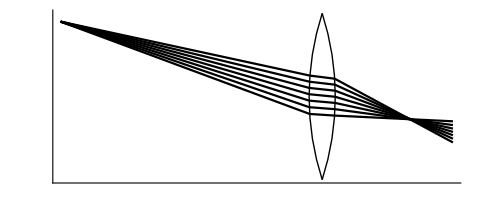

```mathematica
R=100.;a=5.;n1=n3=1;n2=3;yb=√(a*(2R-a));
θm=20π/180.0;y0=0.9yb;light={};
Do[
k1={Cos[θ0],-Sin[θ0]};p1={-R,y0};
equ1={ y==p1[[2]]+k1[[2]]/k1[[1]]*(z-p1[[1]]),
y^2+(z-R+a)^2==R^2 };
s=Solve[equ1,{z,y}];
m=z/.s;s=Select[s,(z/.#)==Min[m]&];
p2={z,y}/.s[[1]];
k=
(n1*k1[[2]]*
(p2[[2]]*k1[[2]]+(p2[[1]]-R+a)*k1[[1]])+
(n2-n1)*p2[[2]])/
(n1*k1[[1]]*
(p2[[2]]*k1[[2]]+(p2[[1]]-R+a)*k1[[1]])+
(n2-n1)*(p2[[1]]-R+a));
kz=1/√(1+k^2);ky=k*kz;k2={kz,ky};
equ2={y==p2[[2]]+k2[[2]]/k2[[1]]*(z-p2[[1]]),
y^2+(z+R-a)^2==R^2};
s=Solve[equ2,{z,y}];
m=z/.s;s=Select[s,(z/.#)==Max[m]&];
p3={z,y}/.s[[1]];
k=
(n2*k2[[2]]*
(p3[[2]]*k2[[2]]+(p3[[1]]+R-a)*k2[[1]])+
(n3-n2)*p3[[2]])/
(n2*k2[[1]]*
(p3[[2]]*k2[[2]]+(p3[[1]]+R-a)*k2[[1]])+
(n3-n2)*(p3[[1]]+R-a));
y=p3[[2]]+k*(z-p3[[1]]);
p4={z,y}/.z->R/2;
g=Show[Graphics[{Thickness[0.004],Line[{p1,p2,p3,p4}]}]];
AppendTo[light,g];Clear[y,z],
{θ0,0.6*θm,θm,θm/15}]
θ=ArcSin[yb/R];
Show[light,Axes->True,Ticks->None,
Epilog->{Circle[{R-a,0},R,{π-θ,π+θ}],
Circle[{-R+a,0},R,{-θ,θ}]},
PlotRange->{{-R,R/2},{-yb,yb}},
AxesStyle->Thickness[0.003]]
Clear[R,a,y0,y,z,equ1,equ2,light,g,s]
```